```mathematica
CloseKernels[];
LaunchKernels[8];
<<SpinWeightedSpheroidalHarmonics`
<<KerrGeodesics`
<<GeneralRelativityTensors`
<<Teukolsky`
ParallelNeeds["SpinWeightedSpheroidalHarmonics`"]
ParallelNeeds["KerrGeodesics`"]
ParallelNeeds["GeneralRelativityTensors`"]
ParallelNeeds["Teukolsky`"]
prec=60;
```

```mathematica
αstring=Import["C:\\Users\\SMP22EJG\\Documents\\GitHub\\ConservativeSelfForce\\Notebooks\\TPPM\\TPPMStringTable..a0..p20..e0..ra4..rb100..regionH..LMAX20..NMAX0.dat"];
αs =Uncompress[αstring[[1,1]]];
α[s_,l_,m_,n_]:=Uncompress[αs[[If[s==-1,1,2], l,m +l+1,1]]];
```

```mathematica
𝔰[sp_,l_,lp_, m_]:= -sp  Sqrt[(2(2l+1))/(2 lp +1)]ClebschGordan[{l,m},{1,0},{lp,m}] ClebschGordan[{l,-sp} ,{1,sp }, {lp ,0}]
Ccoef[s_,j_,k_,m_,bs_]:=𝔰[s,j,k,m]*(j/.bs);
CLcoef [a_,m_,n_,j_,k_,ω_, bs_]:=(j/.bs)*(Sqrt[j(j+1)] KroneckerDelta[j,k] - a ω 𝔰[+1, j,k,m]);
```

```mathematica
Fr0[a_,τ_,  orbit_, k_,m_,n_, LMAX_]:= Module[{A,B,t, r,θ,φ,K0,Σ,Δ},
{t,r,θ,φ}=orbit["Trajectory"];
Δ=r[τ]^2-2 M r[τ] + a^2/.M->1;
Σ=r[τ]^2+ a^2 Cos[θ[τ]]^2;
K0= ω[m,n]((r[τ])^2 + a^2)- a m;

Sum[Module[{bsplus,bsminus,χ, g, dP,Β,Pminus, Pplus,Rminus, λ, cl, cp, cm, 𝒟P},
bsplus = SpinWeightedSpheroidalHarmonicS[1,l,m,N[a ω[m,n]],Method->{"SphericalExpansion","NumTerms"->LMAX+1}]["ExpansionCoefficients"] ;
bsminus = SpinWeightedSpheroidalHarmonicS[-1,l,m,N[a ω[m,n]],Method->{"SphericalExpansion","NumTerms"->LMAX+1}]["ExpansionCoefficients"] ;
cl =CLcoef[a, m, n ,j,k,ω[m,n],bsplus];
cp = Ccoef[1, j, k, m , bsplus];
cm = Ccoef[-1, j,k,m, bsminus];

If[cl ==0&&cp==0&&cl==0,0,
λ = SpinWeightedSpheroidalEigenvalue[-1,l,m,a ω[m,n]];
Β= Sqrt[λ^2+ 4 a m ω[m,n] - 4 a^2 ω[m,n]^2];

Pminus= α[-1,l,m,n][r[τ]];
Pplus = α[1,l,m,n][r[τ]]*Δ;
dP =α[-1,l,m,n]'[r[τ]] ;
𝒟P =dP - ⅈ K0/Δ Pminus; 
g= 1/Β (r[τ]𝒟P-Pminus);
χ=Exp[-ⅈ *ω[m,n]*t[τ] + ⅈ *m *φ[τ]];

A = Re[χ(cl g + ⅈ a cp/Β 𝒟P)];
B= Im[χ(cm Pminus - cp*Pplus)];
tmp=(Sqrt[2] (t'[τ] - a φ'[τ]))/(r[τ]^2 Σ)A + (φ'[τ] *(a^2+r[τ]^2) + a t'[τ])/(Sqrt[2] Δ r[τ] Σ)B;
tmp
]
],{l,Max[1,Abs[m]],LMAX}, {j, k-1, k+1}]
]
```

```mathematica
Off[ClebschGordan::tri ]
Off[ClebschGordan::phy]
```

```mathematica
ParallelEvaluate[Off[ClebschGordan::tri ]]
ParallelEvaluate[Off[ClebschGordan::phy]]
```

{Null,Null,Null,Null,Null,Null,Null,Null}

{Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
α[1,1,1,1]'
```

InterpolatingFunction[…]

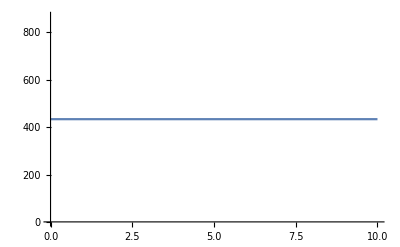

```mathematica
Module[{orbit, t, r, θ,φ},
orbit = KerrGeoOrbit[0,20,0,1]; 
{t,r,θ,φ}=orbit["Trajectory"];

Plot[t'[τ],{τ,0,10}]
]
```

```mathematica
AbsoluteTiming[Module[{t,r,Ε,L,θ,φ, const,a=SetPrecision[0,prec], e=SetPrecision[0,prec],p=SetPrecision[20,prec],x=1, τ=0.5,LMAX= 20,NMax=0},
q=1;
orbit = KerrGeoOrbit[a,p,e,x]; 
{t,r,θ,φ}=orbit["Trajectory"];
Ω =KerrGeoFrequencies[a,p,e,x];
const=KerrGeoConstantsOfMotion[a,p,e,x];
Ε=const[[1]];
L = const[[2]];
Print[Ε];
Print[L];
ω[m_,n_]:=m Ω[[3]] + n Ω[[1]];
(*-1 for Horizon 1 for Infinity*)
reg1 =-1((Ε r[τ](a^2 + r[τ]^2) + 2 a M (a Ε - L))/(2(a^2-2 M r[τ] + r[τ]^2) (r[τ](a^2 + L^2)+ 2 a^2 M + r[τ]^3)))/.M->1; 
reg1S = -(Ε r[τ])/(2 (r[τ] - 2M)(L^2+r[τ]^2))/.M->1;
Fr0ℰS = 2 Ε^2 L^2 r[τ]^3+(L^2+r[τ]^2)(2 L^2+ r[τ]^2)(2M - r[τ])/.M->1;
Fr0𝒦S = Ε^2 r[τ]^5+ r[τ]^2(L^2+r[τ]^2)(r[τ]-2M)/.M->1;
ℰ = NIntegrate[(1-k Sin[β]^2)^(1/2),{β,0,π/2}]/.k->L^2/(r[τ]^2+L^2);
𝒦 = NIntegrate[(1-k Sin[β]^2)^(-1/2),{β,0,π/2}]/.k->L^2/(r[τ]^2+L^2);

reg0S = 1/(π r[τ] (r[τ]^2+L^2)^(3/2)(r[τ]-2M))(Fr0ℰS ℰ+ 𝒦 Fr0𝒦S)/.M->1;
Print[reg1S];
Print[reg1];
Print[reg0S];
kmodes =ParallelTable[Sum[Fr0[a,τ,  orbit,k ,m,n, LMAX]SpinWeightedSphericalHarmonicY[0,k,m,θ[τ],0], {m,-k,k}, {n,-NMax, NMax}],{k,1,20}]
]]
```

0.97618706018395277400024080630429574606142641692355501261259

4.8507125007266594703781292423224435589967049710277887463513

NIntegrate::inumr: The integrand √(1-k Sin[β]^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1.5708}}.

NIntegrate::inumr: The integrand 1/(√(1-k Sin[β]^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1.5708}}.

-0.0012804922857351232375003158724670546051731673678781200011122

-0.001280492285735123237500315872467054605173167367878120001112

0.50667

ClebschGordan::phy: ThreeJSymbol[{0,-1},{1,0},{1,1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2,-3},{1,0},{3,3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{4,-5},{1,0},{5,5}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{6,-7},{1,0},{7,7}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{8,-9},{1,0},{9,9}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{9,-10},{1,0},{10,10}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{10,-11},{1,0},{11,11}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{11,-12},{1,0},{12,12}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{0,-1},{1,1},{1,0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2,-3},{1,0},{3,3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{4,-5},{1,0},{5,5}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{6,-7},{1,0},{7,7}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{8,-9},{1,0},{9,9}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{9,-10},{1,0},{10,10}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{10,-11},{1,0},{11,11}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{11,-12},{1,0},{12,12}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{0,-1},{1,0},{1,1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2,-3},{1,0},{3,3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{4,-5},{1,0},{5,5}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{6,-7},{1,0},{7,7}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{8,-9},{1,0},{9,9}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{9,-10},{1,0},{10,10}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{10,-11},{1,0},{11,11}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{11,-12},{1,0},{12,12}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

1.+0. ⅈ

1.+0. ⅈ

1.+0. ⅈ

«3 more identical outputs»

1.-3.55271×10^-15 ⅈ

1.+0. ⅈ

1.+0. ⅈ

1.+0. ⅈ

«4 more identical outputs»

1.-3.55271×10^-15 ⅈ

1.+0. ⅈ

1.

1.+0. ⅈ

1.+0. ⅈ

1.+0. ⅈ

«3 more identical outputs»

1.-3.55271×10^-15 ⅈ

1.

1.+0. ⅈ

1.+0. ⅈ

1.+0. ⅈ

«3 more identical outputs»

1.-3.55271×10^-15 ⅈ

1.+0. ⅈ

1.+0. ⅈ

1.+0. ⅈ

«3 more identical outputs»

1.-3.55271×10^-15 ⅈ

1.+0. ⅈ

1.+0. ⅈ

1.+0. ⅈ

«47 more identical outputs»

1.

1.+0. ⅈ

1.+0. ⅈ

1.+0. ⅈ

1.

1.+0. ⅈ

1.+0. ⅈ

1.

1.+0. ⅈ

1.+0. ⅈ

1.+0. ⅈ

«36 more identical outputs»

1.

1.

1.+0. ⅈ

1.+0. ⅈ

1.

1.+0. ⅈ

1.

1.+0. ⅈ

1.

1.+0. ⅈ

1.

1.+0. ⅈ

1.+0. ⅈ

1.+0. ⅈ

«25 more identical outputs»

1.

1.+0. ⅈ

1.+0. ⅈ

1.

1.+0. ⅈ

1.+0. ⅈ

1.

1.+0. ⅈ

1.+0. ⅈ

1.+0. ⅈ

«10 more identical outputs»

$Aborted

```mathematica
ClebschGordan[{12,-13},{1,0},{13,13}]
```

ClebschGordan::phy: ThreeJSymbol[{12,-13},{1,0},{13,-13}] is not physical.

0

```mathematica
Table[α[-1,l,-4,0][20],{l,4,20}]
```

{0.903659-0.175584 ⅈ,-0.0232112-0.144464 ⅈ,-0.741289+0.101596 ⅈ,0.0185367+0.15508 ⅈ,0.707158-0.0749603 ⅈ,-0.0150666-0.1582 ⅈ,-0.693361+0.0599518 ⅈ,0.0126195+0.159382 ⅈ,0.686266-0.0501154 ⅈ,-0.0108333-0.15987 ⅈ,-0.6821+0.0431156 ⅈ,0.00948074+0.160064 ⅈ,0.679433-0.0378607 ⅈ,-0.00842394-0.160122 ⅈ,-0.677618+0.0337626 ⅈ,0.00757674+0.160112 ⅈ,0.676326-0.0304734 ⅈ}

```mathematica
kmodes
```

{0.,0.0033274,0.,0.00436327,0.,0.00499392,0.,0.00546517,8.67362×10^-19,0.00585435,0.,0.00619685,0.,0.00651263,0.,0.00681453,0.,0.00711164,0.,0.00738318}

```mathematica
data = Table[{Log[i],Log[Abs[kmodes[[i]]]]},{i,1,20}];
fit = Fit[data, {1,y},y]
```

-6.49941+1.00063 y

-0.0012804922857351232375003158724670546052

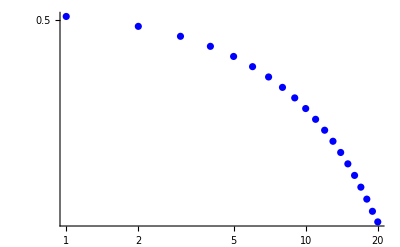

```mathematica
Show[ListLogLogPlot[Table[{l,Abs[kmodes[[l]]-(2l+1)reg1S- reg0S]},{l,1,20}], PlotStyle->Blue], PlotRange->All]
```

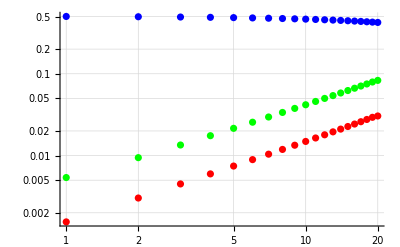

```mathematica
Show[ListLogLogPlot[Table[{l,Abs[kmodes[[l]]-(2l+1)reg1S-reg0S ]},{l,1,20}], PlotStyle->Blue],ListLogLogPlot[Table[{l,Abs[kmodes[[l]]-(2l+1)reg1S ]},{l,1,20}], PlotStyle->Green],ListLogLogPlot[Table[{l,Abs[kmodes[[l]]]},{l,1,20}], PlotStyle->Red], PlotRange->All, GridLines->Automatic]
```

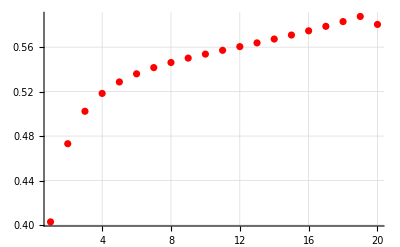

```mathematica
Show[ListPlot[Table[{l,kmodes[[l]]/(-(2l+1)reg1S)},{l,1,20}], PlotStyle->Red], PlotRange->All, GridLines->Automatic]
```

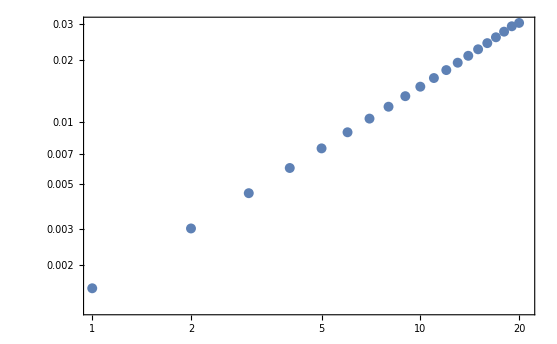

```mathematica
Show[ListLogLogPlot[Table[{l,Abs[kmodes[[l]]]},{l,1,20}], PlotRange->{{1,21},All}, GridLines->Automatic,Frame->True], Plot[fit/.y->l,{l,0,20}]]
```

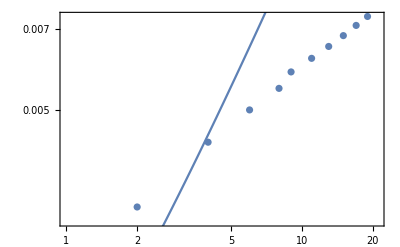

```mathematica
Show[ListPlot[{Abs[{0.,0.003327402467712855,0.,0.0043632684263225485,0.,0.004993918670388048,0.,0.005465167849671059,0.005854345624463611,0.,0.006196853880688058,0.,0.00651263293326262,0.,0.0068145256258632225,0.,0.007111642907866625,0.,0.007383180088632083}]}, PlotRange->{{1,21},All}, ScalingFunctions->{"Log","Log"}, GridLines->Automatic,Frame->True], LogLogPlot[0.001*(l+1/2),{l,1,20}]]
```